```mathematica
rawData=Import[FileNames["data_scenarios_d_*.in",NotebookDirectory[]][[1]],"Table"];
{w,h}=rawData[[1]];
{n,m,r}=rawData[[2]];
buildings=rawData[[3;;3+n-1]];
antennas=rawData[[3+n;;]];
Length[antennas]==m
(*Assert[Length[antennas]==r]*)
```

True

-Graphics-

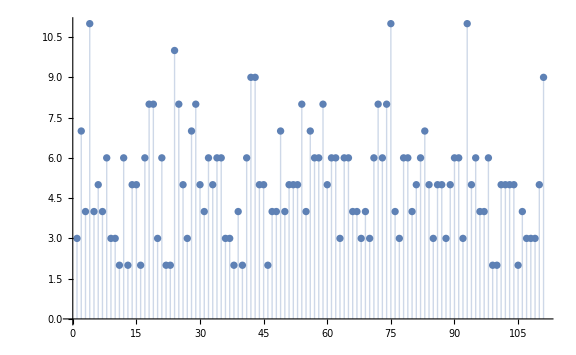

```mathematica
ImageTake[ReplacePixelValue[ConstantImage[0,{w,h}],buildings[[All,{1,2}]]->255],{3,3+110},{54,54+110}]
ListPlot[Total@Transpose@ImageData[%]/255,Filling->Bottom,ImageSize->Large]
```

```mathematica
EstimatedDistribution
```